```mathematica
Clear["Global`*"];
RandomSeed[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
U[x_,y_]=100/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

1001 -23.7129 13.0339 0.921575 0.149737 323.713 300 300 0.000750717 0.00119834 True {1,11} {1,11}

2002 365.256 4.79652 0.9172 0.0972791 7.41528 306.454 372.672 0.00178417 0.00978117 False {1,2,11} {1,11}

3003 300.826 7.1394 0.622132 0.404371 8.02816 308.854 407.207 0.00238098 0.0174193 True {1,5,9,11} {1,11}

4004 408.324 -13.8737 0.768546 0.359542 3.7165 309.757 412.041 0.0028198 0.0221179 False {1,2,11} {1,2,5,6,11}

5005 303.887 5.24988 0.622656 0.441672 6.1724 310.06 411.236 0.00314597 0.024923 True {1,2,3,5,6,9} {1,11}

6006 399.433 4.0688 0.772153 0.252602 11.8026 310.06 411.236 0.00314597 0.024923 False {1,11} {1,11}

7007 305.721 12.196 0.407121 0.456323 4.33843 310.06 411.236 0.00314597 0.024923 True {1,4,5,10,11} {1,11}

8008 406.037 19.7388 0.878057 0.198476 5.19873 310.06 411.236 0.00314597 0.024923 False {1,11} {1,9,11}

9009 302.769 12.1879 0.439127 0.441663 7.29091 310.06 411.236 0.00314597 0.024923 True {1,4,11} {1,11}

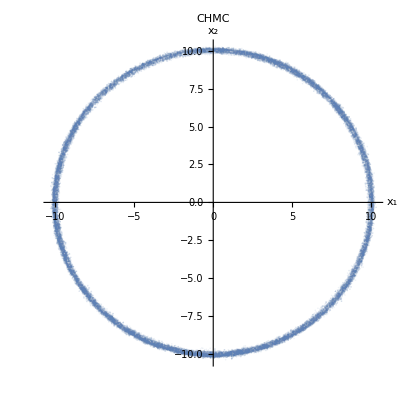

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->CHMC]
```

1001 307.601 10.5136 0.836759 0.269194 3.17019 310.771 300 0.00164765 0.00001 True {1,3,5,10,11} {1,11}

2002 304.876 6.21899 0.584751 0.398046 8.96501 313.841 300 0.00250243 0.00001 True {1,4,9,11} {1,11}

3003 311.695 15.0738 0.601221 0.409646 2.76545 314.46 300 0.00279189 0.00001 True {1,3,11} {1,11}

4004 308.498 12.4161 0.57791 0.429872 6.58303 315.081 300 0.00268295 0.00001 True {1,5,6,11} {1,11}

5005 307.87 5.0343 0.6453 0.381107 9.07233 316.943 300 0.00268295 0.00001 True {1,6,11} {1,11}

6006 311.048 9.29081 0.391738 0.488199 5.89465 316.943 300 0.00268295 0.00001 True {1,4,6,11} {1,11}

7007 313.743 10.9708 0.644389 0.387551 3.19964 316.943 300 0.00268295 0.00001 True {1,2,5,6,9,11} {1,11}

8008 313.656 24.23 0.608511 0.42856 3.28628 316.943 300 0.00268295 0.00001 True {1,3,6,8,9,11} {1,11}

9009 312.057 12.3286 0.483409 0.418001 4.88591 316.943 300 0.00268295 0.00001 True {1,5,11} {1,5,11}

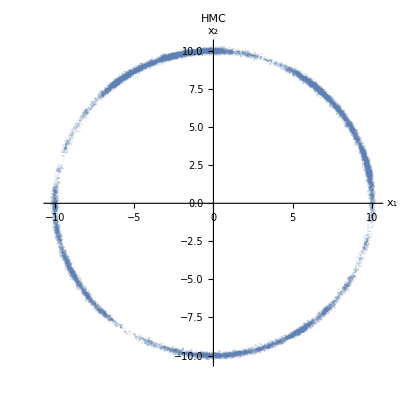

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.1],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->HMC]
```

```mathematica
U[x_,y_]=1/2(√(x^2+y^2)-10)^2;
dU[x_,y_]=GradientG[U[x,y],{x,y}];
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
QS=hmc[U,dU,ddU,2,5000,10000,False,False];
ListPlot[QS,AspectRatio->1,PlotStyle->Opacity[0.5],AxesLabel->{"x_1","x_2"},PlotStyle->{Green},PlotLabel->RHMC]
```

1001 317.032 40.2996 0.668845 0.264724 15.9058 300 332.938 0.00001 0.016907 False {1,2,4,11} {1,11}